## VEKTORJI

ℝ^n je množica {(x_1, x_2, ... , x_n); x_1, x_2, ... , x_n ∈ ℝ} n - teric.

```mathematica
npr. ℝ^2 = {(x, y); x, y ∈ ℝ}
(1, 4) ∈ ℝ^2
```

```mathematica
Vektorje pravzaprav označujemo kot matrike velikosti ℝ^(n×1).
```

```mathematica
MatrixForm[{1,2}]
```

(1
2)

```mathematica
ColumnForm[{1, 2}]
```

1
2

```mathematica
Vektor je usmerjena daljica od neke začetne točke do neke končne točke v ℝ^n.
```

```mathematica
ClearAll[vektor]
```

```mathematica
vektor = {{0,1},{5,4}}
```

{{0,1},{5,4}}

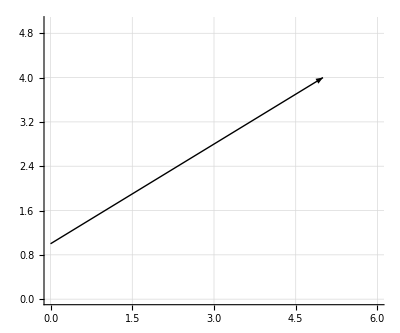

```mathematica
Graphics[Arrow[{vektor}],
Axes->True,
PlotRange->{{0,6},{0,5}}, 
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
Dva vektorja sta enaka, če obstaja tak vporedni premik prostora, da se začetna točka prvega vektorja 
slika v začetno točko drugega vektorja, končna točka prvega vektorja pa v končno točko drugega 
vektorja.
```

```mathematica
ClearAll[vektor1, vektor2]
```

{{0,1},{3,4}}

{{0,-1},{3,2}}

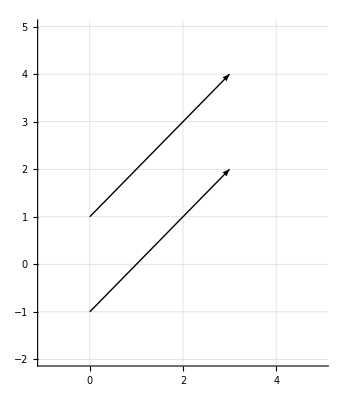

```mathematica
vektor1 = {{0,1},{3,4}}
vektor2 = {{0,-1},{3,2}}
Graphics[Arrow[{vektor1, vektor2}],
Axes->True,
PlotRange->{{-1,5},{-2,5}}, 
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
Zato lahko vsak vektor premaknemo tako, da je njegova začetna točka v izhodišču koordinatnega 
sistema, torej v točki s koordinatami (0, 0, ... , 0).V tem primeru je vsak vektor določen z njegovo
končno točko.
```

```mathematica
MatrixForm[{-3,5}]
```

(-3
5)

```mathematica
ClearAll[vektor3]
```

```mathematica
vektor3 = {{0,0},{-3,5}}
```

{{0,0},{-3,5}}

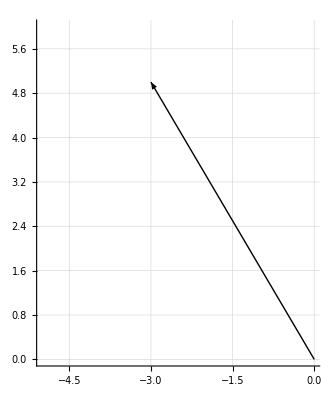

```mathematica
Graphics[Arrow[{vektor3}],
Axes->True,
PlotRange->{{-5,0},{0,6}}, 
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
Če je začetna točka in končna točka vektorja enaka, potem vektorju rečemo ničelni vektor.
Dva vektorja imata isto smer, če je njuna končna točka na istem poltraku iz izhodišča. 
Če pa je njuna končna točka na nasportnih poltrakih, rečemo da imata vektorja nasportno smer.
```

```mathematica
ClearAll[vektor4,vektor5,vektor6]
```

{{0,0},{1,1}}

{{0,0},{3,3}}

{{0,0},{-2,-2}}

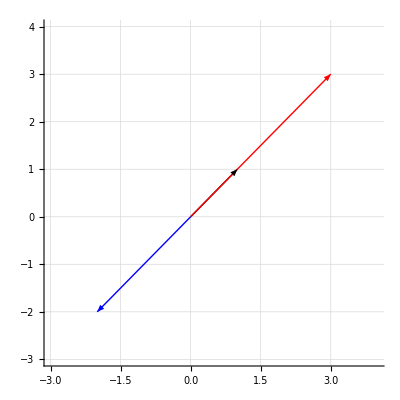

```mathematica
vektor4 = {{0,0},{1,1}}
vektor5 ={{0,0},{3,3}}
vektor6={{0,0},{-2,-2}}
Graphics[{Arrow[{vektor4}],Red,Arrow[{vektor5}],Blue,Arrow[vektor6]},
Axes->True,
PlotRange->{{-3,4},{-3,4}},
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
Operacije na vektorjih
```

```mathematica
1. Seštevanje vektorjev
```

```mathematica
Vsota dveh vektorjev je vektor, ki ima začetno točko v začetni točki prvega vektorja, končno točko pa 
v končni točki drugega vektorja, ob pogoju, da se drugi vektor začne v končni točki prvega vektorja.
```

```mathematica
ClearAll[vektorA ,vektorB,vektorVsote,premaknjeniVektorB]
```

```mathematica
vektorA = {{0,0},{1,2}}
vektorB = {{0,0},{2,-1}}
vektorVsote=a+b
premaknjeniVektorB={{1,2},{3,1}}
```

{{0,0},{1,2}}

{{0,0},{2,-1}}

{{0,0},{3,1}}

{{1,2},{3,1}}

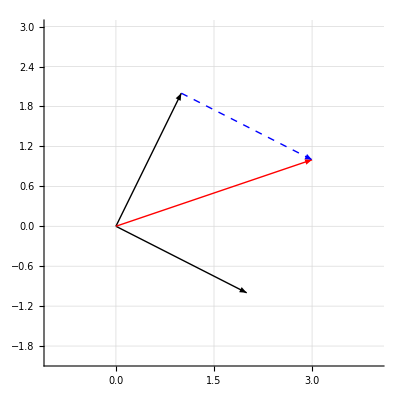

```mathematica
Graphics[{Arrow[{vektorA, vektorB}],Red,Arrow[vektorVsote],Blue,Dashed,Arrow[premaknjeniVektorB]},
Axes->True,
PlotRange->{{-1,4},{-2,3}},
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
2. Množenje vektorja s skalarjem
```

```mathematica
α ∈ ℝ
a ∈ ℝ^n 
Produkt vektorja a = ({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, n]}}) s skalarjem α je vektor, ki mu rečemo α · a = ({{α·Subscript[x, 1]}, {α·Subscript[x, 2]}, {α·Subscript[x, n]}})
```

```mathematica
ClearAll[vektorA,produkt1,produkt2]
```

```mathematica
vektorA = {{0,0},{2,1}}
```

{{0,0},{2,1}}

```mathematica
produkt1 = 2*vektorA
```

{{0,0},{4,2}}

```mathematica
produkt2=1/2*vektorA
```

{{0,0},{1,1/2}}

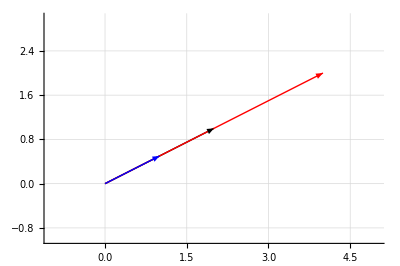

```mathematica
Graphics[{Arrow[vektorA],Red,Arrow[produkt1],Blue,Arrow[produkt2]},
Axes->True,
PlotRange->{{-1,5},{-1,3}} ,
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
3. Skalarni produkt vektorjev
```

```mathematica
a = ({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, n]}}),  b = ({{Subscript[y, 1]}, {Subscript[y, 2]}, {Subscript[y, n]}})


SKALARNI PRODUKT vektorjev a, b je skalar: 
(a, b) = Subscript[x, 1]·Subscript[y, 1] + Subscript[x, 2]·Subscript[y, 2] + ... + Subscript[x, n]·Subscript[y, n]
```

```mathematica
ClearAll[a,b]
```

```mathematica
a = {3,2,4}
```

{3,2,4}

```mathematica
b={1,4,-3}
```

{1,4,-3}

```mathematica
a.b
```

-1

```mathematica
Definirajmo še pojem DOLŽINA oziroma NORMA vektorja a:
||a|| = √(a,a)
```

```mathematica
ClearAll[a]
```

```mathematica
a = {1,-1,4,2,4}
```

{1,-1,4,2,4}

```mathematica
Norm[a]
```

√38

```mathematica
zgled: Izračunaj kot med vektorjema a in b.
```

```mathematica
ClearAll[a,b,skalProdukt,dolžinaA,dolžinaB,kot]
```

```mathematica
a={1,2,-1}
b={3,-1,2}
```

{1,2,-1}

{3,-1,2}

```mathematica
skalProdukt=a.b
```

-1

```mathematica
-1
```

```mathematica
dolžinaA = Norm[a]
```

√6

```mathematica
dolžinaB=Norm[b]
```

√14

```mathematica
kot=(skalProdukt)/(dolžinaA*dolžinaB)
```

-1/(2 √21)

```mathematica
(ArcCos[kot]//N)*180/Pi
```

96.264

```mathematica
Izrek: če sta a in b vektorja v ℝ^n, je (a, b) = ||a|| ||b|| cosϕ. Pri tem je ϕ kot med vektorjema a in b. 
Vzamemo ga lahko na intervalu od 0 do π. Vektorja a in b sta pravokotna, natanko tedaj, ko je (a, b) = 0.
```

```mathematica
4. Vektorski produkt vektorjev
```

```mathematica
a = ({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, n]}}),  b = ({{Subscript[y, 1]}, {Subscript[y, 2]}, {Subscript[y, n]}})


vektorski produkt definiramo kot a × b.
```

```mathematica
ClearAll[a,b]
```

```mathematica
a= {4,1,-1}
b={2,3,1}
```

{4,1,-1}

{2,3,1}

```mathematica
Cross[a,b]
```

{4,-6,10}

```mathematica
5. Mešani produkt vektorjev
```

```mathematica
a, b, c ∈ ℝ^3
Mešani produkt vektorjev a, b, c je [a, b, c] = (a × b, c).
```

```mathematica
ClearAll[a,b,c,vekProdukt,mešaniProdukt]
```

```mathematica
a = {2,1,1}
b={0,1,-3}
c={4,1,0}
```

{2,1,1}

{0,1,-3}

{4,1,0}

```mathematica
vekProdukt=Cross[a,b]
```

{-4,6,2}

```mathematica
mešaniProdukt=vekProdukt.c
```

-10

```mathematica
izrek: Dolžina vektorskega produkta je enaka ploščini paralelograma, ki ga razpenjata vektorja.
```

```mathematica
ClearAll[a,b,vektorja]
```

```mathematica
a={1,3}
b={2,0}
```

{1,3}

{2,0}

{GrayLevel[0],Thickness[Large],Arrow[{{0,0},{1,3}}],Arrow[{{0,0},{2,0}}]}

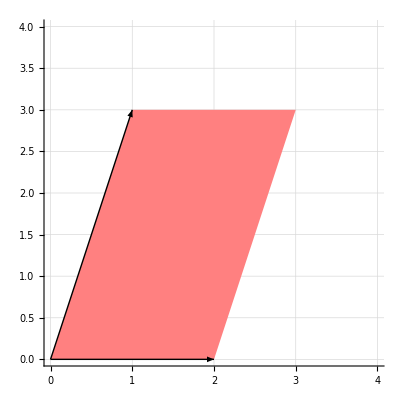

```mathematica
vektorja = {Black,Thick,Arrow[{{0,0},a}],Arrow[{{0,0},b}]}
Graphics[{Pink,Parallelogram[{0,0},{a,b}],vektorja},
Axes->True,
PlotRange->{{0,4},{0,4}},
GridLines->Automatic,
GridLinesStyle->LightGray]
```

```mathematica
S = ||a×b||


Zgled: Izračunaj ploščino trikotnika z oglišči A ( 1, 2, 0), B (3, 4, -1) in C (2, 1, -1)
```

```mathematica
ClearAll[a,b,c,vekProdukt,ploščina ,AB,AC]
```

```mathematica
a = {1,2,0}
b={3,4,-1}
c={2,1,-1}
```

{1,2,0}

{3,4,-1}

{2,1,-1}

```mathematica
trikotnik=Graphics3D[{
{Blue,Triangle[{{1,2,0},{3,4,-1},{2,1,-1}}]},Point[{1,2,0}]},
Axes->True]
```

-Graphics3D-

```mathematica
AB =b-a
```

{2,2,-1}

```mathematica
AC=c-a
```

{1,-1,-1}

```mathematica
vekProdukt=Cross[AB,AC]
```

{-3,1,-4}

```mathematica
ploščina = 0.5*Norm[vekProdukt]
```

2.54951

```mathematica
Izrek: a, b ∈ ℝ^3 je a×b = 0 natanko tedaj, ko a in b kažeta v isto ali nasprotno smer.
```

```mathematica
Izrek: a, b ∈ ℝ^3 je |[a, b, c]| enaka prostornini paralelepipeda, ki ga vektorji a, b, c razpenjajo.
```

```mathematica
Zgled: izračunaj prostornino paralelepipeda, ki ga razpenjajo vektorji A (1, 0, 2), B (-1, 1, 1), C (3, -1, 1).
```

```mathematica
ClearAll[a,b,c,prostorninaParalelepipeda]
```

```mathematica
a = {1,0,2}
b = {-1,1,1}
c={3,-1,1}
```

{1,0,2}

{-1,1,1}

{3,-1,1}

```mathematica
paralelepiped=Parallelepiped[{0,0,0},{{1,0,2},{-1,1,1},{3,-1,1}}]
```

Parallelepiped[{0,0,0},{{1,0,2},{-1,1,1},{3,-1,1}}]

```mathematica
Graphics3D[paralelepiped,Axes->True]
```

-Graphics3D-

```mathematica
vektorskiProdukt = Cross[a,b]
```

{-2,-3,1}

```mathematica
prostorninaParalelepipeda= vektorskiProdukt.c
```

-2

```mathematica
Posledica: Vektorji a, b, c ležijo v isti ravnini natanko tedaj, ko je njihov mešani produkt [a, b, c] = 0
```

```mathematica
Zgled: Ali vektorji A (4, -1, 2), B (-3, 1, 0), C (11, -3, 4)
```

```mathematica
ClearAll[a,b,c,mešaniProdukt,prostornina ]
```

```mathematica
a = {4,-1,2}
b = {-3,1,0}
c={11,-3,4}
```

{4,-1,2}

{-3,1,0}

{11,-3,4}

```mathematica
paralelepiped=Parallelepiped[{0,0,0},{{4,-1,2},{-3,1,0},{11,-3,4}}]
Graphics3D[{paralelepiped},Axes->True]
```

Parallelepiped[{0,0,0},{{4,-1,2},{-3,1,0},{11,-3,4}}]

-Graphics3D-

```mathematica
mešaniProdukt = Cross[a,b]
```

{-2,-6,1}

```mathematica
prostornina=mešaniProdukt.c
```

0

```mathematica
Zgled: izračunaj prostornino tetraedra z oglišči A (2, 2, 1), B (3, -1, 4), C (1, 0, -1), D (4, -1, -3)
```

```mathematica
ClearAll[a,b,c,d,ac,ad,mešaniProdukt,ploščinaTetraedra,ploščinaParalelepipeda]
```

```mathematica
a = {2,2,1}
b = {3,-1,4}
c={1,0,-1}
d={4,-1,-3}
```

{2,2,1}

{3,-1,4}

{1,0,-1}

{4,-1,-3}

```mathematica
Graphics3D[Tetrahedron[{{2,2,1},{3,-1,4},{1,0,-1},{4,-1,-3}},VertexColors->{Red,Green,Blue}], Axes->True]
```

-Graphics3D-

```mathematica
ab=b-a
```

{1,-3,3}

```mathematica
ac=c-a
```

{-1,-2,-2}

```mathematica
ad=d-a
```

{2,-3,-4}

```mathematica
mešaniProdukt=Cross[ab,ac]
```

{12,-1,-5}

```mathematica
ploščinaParalelepipeda=mešaniProdukt.ad
```

47

```mathematica
ploščinaTetraedra=ploščinaParalelepipeda/6
```

47/6

```mathematica
PREMICE IN RAVNINE
```

```mathematica
premica je množica točk {r A + t s; t ∈ ℝ}
A .... neka točka na premici
s .... nek vektor na premici (smerni vektor premice)
t .... parameter


zgled: zapiši premico skozi točki A (1, 2, -1), B (3, -1, 5)
```

```mathematica
ClearAll[a,b,rA,smerniVektor]
```

```mathematica
a = {1,2,-1}
b={3,-1,5}
```

{1,2,-1}

{3,-1,5}

```mathematica
Graphics3D[{{PointSize[0.02],Point[{a,b}]}, InfiniteLine[{{1,2,-1},{3,-1,5}}]}, PlotRange->{{-5,6},{-5,6}, {-5,6}}, Axes->True]
```

-Graphics3D-

```mathematica
smerniVektor=b-a
```

{2,-3,6}

```mathematica
rA=a
```

{1,2,-1}

```mathematica
Zapis premice v parametrični obliki:
```

```mathematica
ClearAll[premica,x1,y1,z1,smerniVektor,a,b]
```

```mathematica
a = {1,2,-1}
b={3,-1,5}
smerniVektor=b-a
```

{1,2,-1}

{3,-1,5}

{2,-3,6}

```mathematica
premica=a+t smerniVektor
```

{1+2 t,2-3 t,-1+6 t}

```mathematica
prva=premica//First
```

1+2 t

```mathematica
druga=Take[premica,{2,2}]//First
```

2-3 t

```mathematica
tretja=premica//Last
```

-1+6 t

```mathematica
Zapis premice v parametrični obliki:
```

```mathematica
ClearAll[x,y,z]
```

```mathematica
Solve[prva==x,t]//First//First
```

t→1/2 (-1+x)

```mathematica
Solve[druga==y,t]//First//First
```

t→(2-y)/3

```mathematica
Solve[tretja==z,t]//First//First
```

t→(1+z)/6

```mathematica
Izrek: Dve premici sta vzporedni natanko tedaj, ko je vektorski produkt njunih smernih vektorjev enak 0.
Zgled: ali sta premici p: (x-1)/3 = (2-y)/4 = z in q: (x+1)/6 = y/8 = (2z-1)/4 vzporedni?
```

```mathematica
ClearAll[x,y,z,vekProdukt,x1,y1,z1,p,o,l,točkaA1,točkaA2,točkaB1,točkaB2,smerniVektor1,smerniVektor2]
```

```mathematica
p=x/.Solve[(x-1)/3==t,x]//First
```

1+3 t

```mathematica
o=y/.Solve[(2-y)/4==t,y]//Simplify//First
```

2-4 t

```mathematica
l=z/.Solve[z==t,z]//First
```

t

```mathematica
smerniVektor1={p[[2]]/.t->1,o[[2]]/.t->1,l/.t->1}
```

{3,-4,1}

```mathematica
točkaA1={p[[1]],o[[1]],0}
```

{1,2,0}

```mathematica
točkaA2= smerniVektor1-točkaA1
```

{2,-6,1}

```mathematica
x1=x/.Solve[(x+1)/6==t,x]//First
```

-1+6 t

```mathematica
y1=y/.Solve[y/8==t,y]//First
```

8 t

```mathematica
z1=z/.Solve[(2z-1)/4==t,z]//Simplify//First
```

1/2+2 t

```mathematica
smerniVektor2={x1[[2]]/.t->1,y1[[1]]/.t->1,z1[[2]]/.t->1}
```

{6,8,2}

```mathematica
točkaB1={x1[[1]],0,z1[[1]]}
```

{-1,0,1/2}

```mathematica
točkaB2=smerniVektor2-točkaB1
```

{7,8,3/2}

```mathematica
vekProdukt=Cross[smerniVektor1,smerniVektor2]
```

{-16,0,48}

```mathematica
Graphics3D[{{InfiniteLine[{točkaA1,točkaA2}]}, InfiniteLine[{točkaB1,točkaB2}]}, PlotRange->{{-4,4},{-4,4}, {-4,4}}, Axes->True]
```

-Graphics3D-

```mathematica
Zgled: ali se premici p: (x-1)/3 = (y+2)/7, z = 1 in q: x = (y+4)/2 = (z-2)/-1 sekata?
```

```mathematica
ClearAll[x,y,z,x1,y1,z1,x2,y2,z2,smerniVektor1,smerniVektor2,tsNeznanki,presečišče,točka1,točkaA2,točkaB2,točkaB1]
```

```mathematica
x1=x/. First[First[Solve[{(x-1)/3== t},x]]]
```

1+3 t

```mathematica
y1=y/.First[First[Solve[{(y+2)/7==t},y]]]
```

-2+7 t

```mathematica
z1=1
```

1

```mathematica
smerniVektor1={x1[[2]]/.t->1,y1[[2]]/.t->1,0}
```

{3,7,0}

```mathematica
x2= x/.First[Solve[{x== s},x]]
```

s

```mathematica
y2=y/.First[Solve[{(y+4)/2==s},y]]
```

2 (-2+s)

```mathematica
z2=z/.First[Solve[{(z-2)/-1==s},z]]
```

2-s

```mathematica
smerniVektor2={1,y2[[1]]/.s->1,z2[[2]]/.s->1}
```

{1,2,-1}

```mathematica
tsNeznanki={t,s}/.First[Solve[x1==x2 && y1 ==  y2 && z1 == z2,{t,s}]]
```

{0,1}

```mathematica
presečišče= {x1 /.{t -> tsNeznanki[[1]]},y1 /.{t -> tsNeznanki[[1]]},z1 /.{t -> tsNeznanki[[1]]}}
```

{1,-2,1}

```mathematica
točkaA1={x1[[1]],y1[[1]],z1}
```

{1,-2,1}

```mathematica
točkaB1= točkaA1-smerniVektor1
```

{-2,-9,1}

```mathematica
točkaA2={0,-4,z2[[1]]}
```

{0,-4,2}

```mathematica
točkaB2=točkaA2-smerniVektor2
```

{-1,-6,3}

```mathematica
Graphics3D[{InfiniteLine[{točkaA1,točkaB1}], InfiniteLine[{točkaA2,točkaB2}],{PointSize[0.02],Point[presečišče]}}, PlotRange->{{-4,4},{-4,4}, {-4,4}}, Axes->True]
```

-Graphics3D-

```mathematica
n ... vektor, pravokoten na ravnino (normalni vektor oziroma vektor normale)
enačba ravnine z normalo (a, b, c): ax + by + cz = d
```

```mathematica
zgled: ali premica p: (x+1)/3 = (1+y)/4 = 2z seka ravnino π: x + y - 3z = 4
```

```mathematica
ClearAll[x1,y1,z1,t,u,točkaA,točkaB,enačbaRavnine,smerniVektor,neznankaT,presečišče,ravnina]
```

```mathematica
ravnina={{1,0,-1},{5,2,1}}
```

{{1,0,-1},{5,2,1}}

```mathematica
y1=y/.First[Solve[{(1+y)/4==t},y]]
```

-1+4 t

```mathematica
x1=x/.First[Solve[(x+1)/3==t,x]]
```

-1+3 t

```mathematica
z1=z/.First[Solve[2z==t,z]]
```

t/2

```mathematica
točkaA={x1[[1]],y1[[1]],0}
```

{-1,-1,0}

```mathematica
smerniVektor={x1[[2]]/.t->1,y1[[2]]/.t->1,z1[[1]]}
```

{3,4,1/2}

```mathematica
točkaB=smerniVektor-točkaA
```

{4,5,1/2}

```mathematica
enačbaRavnine=First[{x+y-3z==4}/.{x->x1,y->y1,z->z1}//FullSimplify]
```

11 t==12

```mathematica
neznankaT = t/.First[Solve[enačbaRavnine,t]]
```

12/11

```mathematica
presečišče1={x1/.t->neznankaT,y1/.t->neznankaT,z1/.t->neznankaT}
```

{25/11,37/11,6/11}

```mathematica
Graphics3D[{{ PointSize[0.02],Green,Point[presečišče1]},
InfiniteLine[presečišče1,točkaA],
Hyperplane[{3,4,-1},presečišče1]}, 
PlotRange->{{-10,10},{-10,10}, {-10,10}}, 
Axes->True]
```

-Graphics3D-